```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/NeuPhysics/aNN/MMA

ANN Construction of Homogeneous Gas Model

Define two density matrices

```mathematica
rho[t_]={{r11[t],r12[t]},{r21[t],r22[t]}};
%//MatrixForm
rhob[t_]={{rb11[t],rb12[t]},{rb21[t],rb22[t]}};
%//MatrixForm
```

(r11[t] | r12[t]
r21[t] | r22[t])

(rb11[t] | rb12[t]
rb21[t] | rb22[t])

To write down the decomposition of density matrice, I could just find the four equations. To do so I need the following matrices

```mathematica
Clear[bM11,bM12,bM21,bM22]
bM=1/2{{bM11,bM12},{bM21,bM22}};
%//MatrixForm
elM={{1,0},{0,0}};
%//MatrixForm
```

(bM11/2 | bM12/2
bM21/2 | bM22/2)

(1 | 0
0 | 0)

```mathematica
Clear[hbar,delm2E,lambda,gF]
hbar=1;
delm2E; (*This is deltam^2/2E*)
lambda;
gF;
```

## Homogeneous Gas

Define Hamiltonians

```mathematica
(*Clear[hamil,hamilb]*)
hamil[t_]=delm2E bM +lambda elM + Sqrt[2]gF(rho[t]-rhob[t]);
%//MatrixForm
hamilb[t_]=-delm2E bM +lambda elM + Sqrt[2]gF(rho[t]-rhob[t]);
%//MatrixForm
```

(0.806351+√2 (r11[t]-rb11[t]) | 0.158114+√2 (r12[t]-rb12[t])
0.158114+√2 (r21[t]-rb21[t]) | 0.193649+√2 (r22[t]-rb22[t]))

(1.19365+√2 (r11[t]-rb11[t]) | -0.158114+√2 (r12[t]-rb12[t])
-0.158114+√2 (r21[t]-rb21[t]) | -0.193649+√2 (r22[t]-rb22[t]))

The two eqns are

```mathematica
Clear[lhs,rhs]
lhs=I hbar D[rho[t],t]//FullSimplify;
rhs=hamil[t].rho[t]-rho[t].hamil[t]//FullSimplify;
lhs//MatrixForm;
rhs//MatrixForm;
-lhs+rhs//MatrixForm
```

(r21[t] (0.158114-1.41421 rb12[t])+r12[t] (-0.158114+1.41421 rb21[t])-ⅈ r11'[t] | r22[t] (0.158114-1.41421 rb12[t])+r11[t] (-0.158114+1.41421 rb12[t])+r12[t] (0.612702-1.41421 rb11[t]+1.41421 rb22[t])-ⅈ r12'[t]
r11[t] (0.158114-1.41421 rb21[t])+r22[t] (-0.158114+1.41421 rb21[t])+r21[t] (-0.612702+1.41421 rb11[t]-1.41421 rb22[t])-ⅈ r21'[t] | r21[t] (-0.158114+1.41421 rb12[t])+r12[t] (0.158114-1.41421 rb21[t])-ⅈ r22'[t])

```mathematica
Clear[lhsb,rhsb]
lhsb=I hbar D[rhob[t],t]//FullSimplify;
rhsb=hamilb[t].rhob[t]-rhob[t].hamilb[t]//FullSimplify;
lhsb//MatrixForm;
rhsb//MatrixForm;
-lhsb+rhsb//MatrixForm
```

((0.158114-1.41421 r21[t]) rb12[t]+(-0.158114+1.41421 r12[t]) rb21[t]-ⅈ rb11'[t] | (0.158114-1.41421 r12[t]) rb11[t]+(1.3873+1.41421 r11[t]-1.41421 r22[t]) rb12[t]+(-0.158114+1.41421 r12[t]) rb22[t]-ⅈ rb12'[t]
(-0.158114+1.41421 r21[t]) rb11[t]+(-1.3873-1.41421 r11[t]+1.41421 r22[t]) rb21[t]+(0.158114-1.41421 r21[t]) rb22[t]-ⅈ rb21'[t] | (-0.158114+1.41421 r21[t]) rb12[t]+(0.158114-1.41421 r12[t]) rb21[t]-ⅈ rb22'[t])

```mathematica
(lhsb-rhsb)[[1]][[1]]
```

-(0.158114-1.41421 r21[t]) rb12[t]-(-0.158114+1.41421 r12[t]) rb21[t]+ⅈ rb11'[t]

```mathematica
mattemp={{0,1},{2,3}}
mattemp.mattemp
```

{{0,1},{2,3}}

{{2,3},{6,11}}

## Solving Exactly The Same Problem in HomogeneousModel.ipynb

Exactly the same one.

```mathematica
delm2E=1; (*This is deltam^2/2E or I would rather say omega*)
lambda=1;
gF=1;
bM11=-0.38729833462;
bM12=0.31622776601;
bM21=0.31622776601;
bM22=0.38729833462;
```

```mathematica
hamil[t]//MatrixForm
hamilb[t]//MatrixForm
```

(0.806351+√2 (r11[t]-rb11[t]) | 0.158114+√2 (r12[t]-rb12[t])
0.158114+√2 (r21[t]-rb21[t]) | 0.193649+√2 (r22[t]-rb22[t]))

(1.19365+√2 (r11[t]-rb11[t]) | -0.158114+√2 (r12[t]-rb12[t])
-0.158114+√2 (r21[t]-rb21[t]) | -0.193649+√2 (r22[t]-rb22[t]))

```mathematica
systemN =Flatten[I hbar D[rho[t],t]-hamil[t].rho[t]+rho[t].hamil[t]];
%//MatrixForm
systemNb = Flatten[I hbar D[rhob[t],t]-hamilb[t].rhob[t]+rhob[t].hamilb[t]];
%//MatrixForm
```

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t])

(rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t])

```mathematica
init={r11[0]==1,r12[0]==0,r21[0]==0,r22[0]==0,rb11[0]==1,rb12[0]==0,rb21[0]==0,rb22[0]==0};
system=Flatten@{systemN,systemNb};
%//MatrixForm
systemEqn=Table[system[[i]]==0,{i,1,Length@system}];
%//MatrixForm
systemFull=Flatten@{systemEqn,init};
%//MatrixForm
```

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t]
rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t])

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]==0
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]==0
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]==0
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t]==0
rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]==0
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]==0
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]==0
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t]==0)

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]==0
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]==0
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]==0
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t]==0
rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]==0
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]==0
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]==0
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t]==0
r11[0]==1
r12[0]==0
r21[0]==0
r22[0]==0
rb11[0]==1
rb12[0]==0
rb21[0]==0
rb22[0]==0)

```mathematica
sol=NDSolve[systemFull,{r11,r12,r21,r22,rb11,rb12,rb21,rb22},{t,0,5}]
```

{{r11→InterpolatingFunction[{{0., 5.}}, <>],r12→InterpolatingFunction[{{0., 5.}}, <>],r21→InterpolatingFunction[{{0., 5.}}, <>],r22→InterpolatingFunction[{{0., 5.}}, <>],rb11→InterpolatingFunction[{{0., 5.}}, <>],rb12→InterpolatingFunction[{{0., 5.}}, <>],rb21→InterpolatingFunction[{{0., 5.}}, <>],rb22→InterpolatingFunction[{{0., 5.}}, <>]}}

```mathematica
Evaluate[r11[1]/.sol]
```

{0.926851+0. ⅈ}

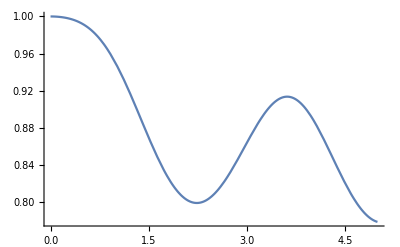

```mathematica
Plot[Evaluate[rb11[t]/.sol],{t,0,5},PlotRange->All]
```

```mathematica
MMAoptpltdata=Flatten@Table[Re@Evaluate[rb11[t]/.sol],{t,0,5,1/100}];
Export["../ipynb/assets/homogen/MMA_optmize_pltdata.txt",MMAoptpltdata]
```

../ipynb/assets/homogen/MMA_optmize_pltdata.txt

Compare data
with
/assets/homogen/optimize_ResultSLSQP240.txt

```mathematica
(*
datar11=Flatten@Import["../ipynb/assets/homogen/optimize_pltdatar11.txt","Table"]
datar11t=Table[i,{i,0,5,1/100}];
Length@data1r11

Length@datar11t

ListPlot[data1r11,Joined->True]
*)
```

{1.,1.00666019474245161,1.01222438671607362,1.01662401367314126,1.0197931235213038,1.02166934200181991,1.02219488948867587,1.02131763338217385,1.01899216006739368,1.01518084803588859,1.00985492162361212,1.00299546299697795,0.994594358617172603,0.984655155518121106,0.973193802421624343,0.960239251043924824,0.945833893961965488,0.93003381712470623,0.912908847513679955,0.894542379556252154,0.87503096763605992,0.854483676375035417,0.833021185216662352,0.810774649149280546,0.787884323093256067,0.764497963451327589,0.740769026491412852,0.716854689483183538,0.692913726707658939,0.669104278434749067,0.645581556510535726,0.622495535065640704,0.599988678760931649,0.578193763611040135,0.557231846444822598,0.537210438169580362,0.518221932952481201,0.500342340062651658,0.483630357408339484,0.4681268158960743,0.4538545119546471,0.440818432406771099,0.429006361992490759,0.418389850019608378,0.408925499655223179,0.400556532072440463,0.393214568720849478,0.386821568924568093,0.381291857136345724,0.376534174555221868,0.372453693271113107,0.368953937238523766,0.365938562642283083,0.363312959933815405,0.36098565028194296,0.358869459717801265,0.356882464258613363,0.354948708286216053,0.352998706088565317,0.350969742544375296,0.348805993375130852,0.346458488252094354,0.343884941464710603,0.34104947502807903,0.337922258262122854,0.334479086255611069,0.330700917467846023,0.326573388231477968,0.322086319283198974,0.317233226812221436,0.312010847991988971,0.306418688628278479,0.300458598467661431,0.294134377890844623,0.28745141817304154,0.280416376221267361,0.273036883678872244,0.265321289497034152,0.257278434483906637,0.248917455926212172,0.240247620107106319,0.231278180391939037,0.222018258495716436,0.212476746561897412,0.202662227752777979,0.192582913162141933,0.18224659299792223,0.171660600136311792,0.160831784310731529,0.149766495362986696,0.138470574145293845,0.126949349816970369,0.115207642426270573,0.10324976980454148,0.0910795579257468457,0.0787003539991451007,0.0661150416665539087,0.053326057768509183,0.0403354102263000502,0.0271446966599491191}

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

### Vacuum Case

Vacuum

```mathematica
(*Clear[hamil,hamilb]*)
hamilv[t_]=delm2E bM ;
%//MatrixForm
hamilvb[t_]=-delm2E bM ;
%//MatrixForm
```

(-0.193649 | 0.158114
0.158114 | 0.193649)

(0.193649 | -0.158114
-0.158114 | -0.193649)

```mathematica
Clear[lhsv,rhsv]
lhsv=I hbar D[rho[t],t]//FullSimplify;
rhsv=hamilv[t].rho[t]-rho[t].hamilv[t]//FullSimplify;
lhsv//MatrixForm;
rhsv//MatrixForm;
-lhsv+rhsv//MatrixForm

Clear[lhsvb,rhsvb]
lhsvb=I hbar D[rhob[t],t]//FullSimplify;
rhsvb=hamilvb[t].rhob[t]-rhob[t].hamilvb[t]//FullSimplify;
lhsvb//MatrixForm;
rhsvb//MatrixForm;
-lhsvb+rhsvb//MatrixForm
```

(0.-0.158114 r12[t]+0.158114 r21[t]-ⅈ r11'[t] | -0.158114 r11[t]-0.387298 r12[t]+0.158114 r22[t]-ⅈ r12'[t]
0.158114 r11[t]+0.387298 r21[t]-0.158114 r22[t]-ⅈ r21'[t] | 0.+0.158114 r12[t]-0.158114 r21[t]-ⅈ r22'[t])

(0.+0.158114 rb12[t]-0.158114 rb21[t]-ⅈ rb11'[t] | 0.158114 rb11[t]+0.387298 rb12[t]-0.158114 rb22[t]-ⅈ rb12'[t]
-0.158114 rb11[t]-0.387298 rb21[t]+0.158114 rb22[t]-ⅈ rb21'[t] | 0.-0.158114 rb12[t]+0.158114 rb21[t]-ⅈ rb22'[t])

```mathematica
hamilv[t]//MatrixForm
hamilvb[t]//MatrixForm
```

(-0.193649 | 0.158114
0.158114 | 0.193649)

(0.193649 | -0.158114
-0.158114 | -0.193649)

```mathematica
hamilv[t].rho[t]-rho[t].hamilv[t]
```

{{0.-0.158114 r12[t]+0.158114 r21[t],-0.158114 r11[t]-0.387298 r12[t]+0.158114 r22[t]},{0.158114 r11[t]+0.387298 r21[t]-0.158114 r22[t],0.+0.158114 r12[t]-0.158114 r21[t]}}

```mathematica
systemvN =Flatten[I hbar D[rho[t],t]-hamilv[t].rho[t]+rho[t].hamilv[t]];
%//MatrixForm
systemvNb = Flatten[I hbar D[rhob[t],t]-hamilvb[t].rhob[t]+rhob[t].hamilvb[t]];
%//MatrixForm
```

(0.+0.158114 r12[t]-0.158114 r21[t]+ⅈ r11'[t]
0.158114 r11[t]+0.387298 r12[t]-0.158114 r22[t]+ⅈ r12'[t]
-0.158114 r11[t]-0.387298 r21[t]+0.158114 r22[t]+ⅈ r21'[t]
0.-0.158114 r12[t]+0.158114 r21[t]+ⅈ r22'[t])

(0.-0.158114 rb12[t]+0.158114 rb21[t]+ⅈ rb11'[t]
-0.158114 rb11[t]-0.387298 rb12[t]+0.158114 rb22[t]+ⅈ rb12'[t]
0.158114 rb11[t]+0.387298 rb21[t]-0.158114 rb22[t]+ⅈ rb21'[t]
0.+0.158114 rb12[t]-0.158114 rb21[t]+ⅈ rb22'[t])

```mathematica
initv={r11[0]==1,r12[0]==0,r21[0]==0,r22[0]==0,rb11[0]==1,rb12[0]==0,rb21[0]==0,rb22[0]==0};
systemv=Flatten@{systemvN,systemvNb};
%//MatrixForm
systemvEqn=Table[systemv[[i]]==0,{i,1,Length@systemv}];
%//MatrixForm
systemvFull=Flatten@{systemvEqn,initv};
%//MatrixForm
```

(1/2 bM21 delm2E r12[t]-1/2 bM12 delm2E r21[t]+ⅈ r11'[t]
1/2 bM12 delm2E r11[t]-1/2 bM11 delm2E r12[t]+1/2 bM22 delm2E r12[t]-1/2 bM12 delm2E r22[t]+ⅈ r12'[t]
-1/2 bM21 delm2E r11[t]+1/2 bM11 delm2E r21[t]-1/2 bM22 delm2E r21[t]+1/2 bM21 delm2E r22[t]+ⅈ r21'[t]
-1/2 bM21 delm2E r12[t]+1/2 bM12 delm2E r21[t]+ⅈ r22'[t]
-1/2 bM21 delm2E rb12[t]+1/2 bM12 delm2E rb21[t]+ⅈ rb11'[t]
-1/2 bM12 delm2E rb11[t]+1/2 bM11 delm2E rb12[t]-1/2 bM22 delm2E rb12[t]+1/2 bM12 delm2E rb22[t]+ⅈ rb12'[t]
1/2 bM21 delm2E rb11[t]-1/2 bM11 delm2E rb21[t]+1/2 bM22 delm2E rb21[t]-1/2 bM21 delm2E rb22[t]+ⅈ rb21'[t]
1/2 bM21 delm2E rb12[t]-1/2 bM12 delm2E rb21[t]+ⅈ rb22'[t])

(1/2 bM21 delm2E r12[t]-1/2 bM12 delm2E r21[t]+ⅈ r11'[t]==0
1/2 bM12 delm2E r11[t]-1/2 bM11 delm2E r12[t]+1/2 bM22 delm2E r12[t]-1/2 bM12 delm2E r22[t]+ⅈ r12'[t]==0
-1/2 bM21 delm2E r11[t]+1/2 bM11 delm2E r21[t]-1/2 bM22 delm2E r21[t]+1/2 bM21 delm2E r22[t]+ⅈ r21'[t]==0
-1/2 bM21 delm2E r12[t]+1/2 bM12 delm2E r21[t]+ⅈ r22'[t]==0
-1/2 bM21 delm2E rb12[t]+1/2 bM12 delm2E rb21[t]+ⅈ rb11'[t]==0
-1/2 bM12 delm2E rb11[t]+1/2 bM11 delm2E rb12[t]-1/2 bM22 delm2E rb12[t]+1/2 bM12 delm2E rb22[t]+ⅈ rb12'[t]==0
1/2 bM21 delm2E rb11[t]-1/2 bM11 delm2E rb21[t]+1/2 bM22 delm2E rb21[t]-1/2 bM21 delm2E rb22[t]+ⅈ rb21'[t]==0
1/2 bM21 delm2E rb12[t]-1/2 bM12 delm2E rb21[t]+ⅈ rb22'[t]==0)

(1/2 bM21 delm2E r12[t]-1/2 bM12 delm2E r21[t]+ⅈ r11'[t]==0
1/2 bM12 delm2E r11[t]-1/2 bM11 delm2E r12[t]+1/2 bM22 delm2E r12[t]-1/2 bM12 delm2E r22[t]+ⅈ r12'[t]==0
-1/2 bM21 delm2E r11[t]+1/2 bM11 delm2E r21[t]-1/2 bM22 delm2E r21[t]+1/2 bM21 delm2E r22[t]+ⅈ r21'[t]==0
-1/2 bM21 delm2E r12[t]+1/2 bM12 delm2E r21[t]+ⅈ r22'[t]==0
-1/2 bM21 delm2E rb12[t]+1/2 bM12 delm2E rb21[t]+ⅈ rb11'[t]==0
-1/2 bM12 delm2E rb11[t]+1/2 bM11 delm2E rb12[t]-1/2 bM22 delm2E rb12[t]+1/2 bM12 delm2E rb22[t]+ⅈ rb12'[t]==0
1/2 bM21 delm2E rb11[t]-1/2 bM11 delm2E rb21[t]+1/2 bM22 delm2E rb21[t]-1/2 bM21 delm2E rb22[t]+ⅈ rb21'[t]==0
1/2 bM21 delm2E rb12[t]-1/2 bM12 delm2E rb21[t]+ⅈ rb22'[t]==0
r11[0]==1
r12[0]==0
r21[0]==0
r22[0]==0
rb11[0]==1
rb12[0]==0
rb21[0]==0
rb22[0]==0)

```mathematica
solv=NDSolve[systemvN,{r11,r12,r21,r22,rb11,rb12,rb21,rb22},{t,0,20}]
```

NDSolve::deqn: Equation or list of equations expected instead of 1/2 bM21 delm2E r12[t] in the first argument 1/2 bM21 delm2E r12[t] - 1/2 bM12 delm2E r21[t] + ⅈ SuperscriptBox[1/2 bM12 delm2E r11[t] - 1/2 bM11 delm2E r12[t] + 1/2 bM22 delm2E r12[t] - 1/2 bM12 delm2E r22[t] + ⅈ SuperscriptBox[« 1 »-1/2 bM21 delm2E r12[t] + 1/2 bM12 delm2E r21[t] + ⅈ SuperscriptBox[.

NDSolve[{1/2 bM21 delm2E r12[t]-1/2 bM12 delm2E r21[t]+ⅈ r11'[t],1/2 bM12 delm2E r11[t]-1/2 bM11 delm2E r12[t]+1/2 bM22 delm2E r12[t]-1/2 bM12 delm2E r22[t]+ⅈ r12'[t],-1/2 bM21 delm2E r11[t]+1/2 bM11 delm2E r21[t]-1/2 bM22 delm2E r21[t]+1/2 bM21 delm2E r22[t]+ⅈ r21'[t],-1/2 bM21 delm2E r12[t]+1/2 bM12 delm2E r21[t]+ⅈ r22'[t]},{r11,r12,r21,r22,rb11,rb12,rb21,rb22},{t,0,20}]

```mathematica
Evaluate[r11[1]/.solv]
```

ReplaceAll::reps: {solv} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

r11[1]/.solv

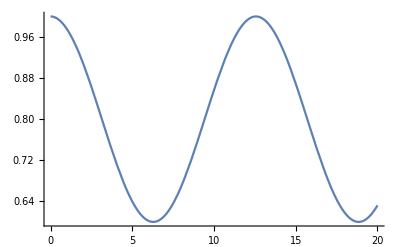

```mathematica
Plot[Evaluate[rb11[t]/.solv],{t,0,20},PlotRange->All]
```

```mathematica
MMAoptpltdataVac=Flatten@Table[Re@Evaluate[rb11[t]/.solv],{t,0,15,1/300}];
Export["../ipynb/assets/homogen/MMA_optmize_Vac_pltdata.txt",MMAoptpltdataVac]
```

../ipynb/assets/homogen/MMA_optmize_Vac_pltdata.txt

### Analytic Stuff

r11[t]->np.sum(initialCondition + ti * v11 * trigf( ti*w11 +u11 ) )

```mathematica
delm2E=1;
analytic=Flatten[I hamilv[t].rho[t]+rho[t].hamilv[t]]/.{r11[t]->initialCondition+ti*v11*trigf[ti*w11+u11],r12[t]->initialCondition+ti*v12*trigf[ti*w12+u12],
r21[t]->initialCondition+ti*v21*trigf[ti*w21+u21],
r22[t]->initialCondition+ti*v22*trigf[ti*w22+u22]};
%//FullSimplify//MatrixForm
Clear[delm2E]
```

(1/2 (((1+ⅈ) bM11+ⅈ bM12+bM21) initialCondition+(1+ⅈ) bM11 ti v11 trigf[u11+ti w11]+bM21 ti v12 trigf[u12+ti w12]+ⅈ bM12 ti v21 trigf[u21+ti w21])
1/2 ((ⅈ bM11+(1+ⅈ) bM12+bM22) initialCondition+bM12 ti v11 trigf[u11+ti w11]+(ⅈ bM11+bM22) ti v12 trigf[u12+ti w12]+ⅈ bM12 ti v22 trigf[u22+ti w22])
1/2 ((bM11+(1+ⅈ) bM21+ⅈ bM22) initialCondition+ⅈ bM21 ti v11 trigf[u11+ti w11]+(bM11+ⅈ bM22) ti v21 trigf[u21+ti w21]+bM21 ti v22 trigf[u22+ti w22])
1/2 ((bM12+ⅈ bM21+(1+ⅈ) bM22) initialCondition+ⅈ bM21 ti v12 trigf[u12+ti w12]+bM12 ti v21 trigf[u21+ti w21]+(1+ⅈ) bM22 ti v22 trigf[u22+ti w22]))

```mathematica
D[analytic,w11]
```

{(1/2+ⅈ/2) bM11 ti^2 v11 trigf'[u11+ti w11],1/2 bM12 ti^2 v11 trigf'[u11+ti w11],1/2 ⅈ bM21 ti^2 v11 trigf'[u11+ti w11],0}